# A Test of How do EoS Change Observables

## Preliminaries

### Observables

A list of the observables in cosmology are shown in CosmologyReserchSurvivingManual.

### EoS parameterization

w=w_0+(w_1(z/(1+z)))^n

w=w_0+w_1 z/(1+z)^n

## Fundamental Definations

### Basic

Hubble constant

```mathematica
H0=71;
```

Speed of light

```mathematica
Clear[speedc]
```

```mathematica
speedc
```

speedc

Hubble distance

```mathematica
dHubble=speedc/H0
```

speedc/71

Give assumptions

### Model FRW

Hubble function

```mathematica
hubble[z_,evo_:1,Ωm0_:0.27,Ωd0_:0.73,Ωr0_:0,Ωk0_:0]:=H0 √(Ωr0 (1+z)^4+Ωm0(1+z)^3+Ωd0 evo)
```

```mathematica
evo[z_,eqost_:-1]:=Exp[3Integrate[(1+eqost)/(1+tmp),{tmp,0,z}]]
```

First time derivative of redshift

```mathematica
dz[z_,evo_:1,Ωm0_:0.27,Ωd0_:0.73,Ωr0_:0,Ωk0_:0]=71 (1+z) √(evo Ωd0+(1+z)^3 Ωm0+(1+z)^4 Ωr0)
```

71 (1+z) √(evo Ωd0+(1+z)^3 Ωm0+(1+z)^4 Ωr0)

Integral of hubble function

```mathematica
intHubble[z_,evo_:1,Ωm0_:0.27,Ωd0_:0.73,Ωr0_:0,Ωk0_:0]:=Integrate[1/hubble[tmp,evo,Ωm0,Ωd0,Ωr0,Ωk0],{tmp,0,z}]/H0
```

Line of sight comoving distance

```mathematica
losDistance[z_,evo_:1,Ωm0_:0.27,Ωd0_:0.73,Ωr0_:0,Ωk0_:0]:=speedc Integrate[1/hubble[tmp,evo,Ωm0,Ωd0,Ωr0,Ωk0],{tmp,0,z}]
```

Angular diameter distance

```mathematica
aglDistance[z_,evo_:1,Ωm0_:0.27,Ωd0_:0.73,Ωr0_:0,Ωk0_:0]:=speedc/(1+z) Integrate[1/hubble[tmp,evo,Ωm0,Ωd0,Ωr0,Ωk0],{tmp,0,z}]
```

### EoS parameterization

#### Reference Model LCDM

```mathematica
hubbleLCDM[z_,Ωm0_:0.27,Ωd0_:0.73,Ωr0_:0]=71  √(Ωd0+(1+z)^3 Ωm0+(1+z)^4 Ωr0)
```

71 √(Ωd0+(1+z)^3 Ωm0+(1+z)^4 Ωr0)

Set up time derivative of redshift

```mathematica
dz[z,1]
```

71 (1+z) √(0.73+0.27 (1+z)^3)

Line of sight comoving distance in LCDM

1/hubbleLCDM[tmp]

1/(71 √(0.73+0.27 (1+tmp)^3))

losDistanceLCDM[z_, Ωm0_: 0.27, Ωd0_: 0.73, Ωr0_: 0] := speedc Integrate[1/hubbleLCDM[tmp], {tmp, 0, z}, Assumptions -> tmp ∈ Reals && tmp > -1 && z ∈ Reals && z > -1]

losDistanceLCDM[1] // Timing

{0.515,(0.0110657-1.40183×10^-18 ⅈ) speedc}

Plot[Log[1/hubbleLCDM[tmp]], {tmp, 0, 2}]

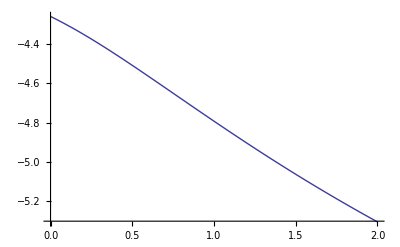

Clear[losDistanceLCDM]

```mathematica
losDistanceLCDM[z_,Ωm0_:0.27,Ωd0_:0.73,Ωr0_:0]:=NIntegrate[1/hubbleLCDM[tmp],{tmp,0,z}]
```

```mathematica
losDistanceLCDM[1]//Timing
```

{0.016,0.0110657}

```mathematica
aglDistanceLCDM[z_,Ωm0_:0.27,Ωd0_:0.73,Ωr0_:0]:=1/(1+z)NIntegrate[1/hubbleLCDM[tmp],{tmp,0,z}]
```

Luminosity distance

```mathematica
luDistanceLCDM[z_,Ωm0_:0.27,Ωd0_:0.73,Ωr0_:0]:=(1+z)NIntegrate[1/hubbleLCDM[tmp],{tmp,0,z}]
```

Look back time

```mathematica
lbTimeLCDM[z_,Ωm0_:0.27,Ωd0_:0.73,Ωr0_:0]:=NIntegrate[1/((1+tmp)hubbleLCDM[tmp]),{tmp,0,z}]
```

#### Constant EoS

```mathematica
evo[z,eqost1]
```

ConditionalExpression[(1+z)^(3 (1+eqost1)),Re[z]≥-1||z∉Reals]

```mathematica
evoCon[z_,eqost1_:-1]=(1+z)^(3 (1+eqost1))
```

(1+z)^(3 (1+eqost1))

```mathematica
evoCon[1,-0.5]
```

2.82843

Hubble equation

```mathematica
hubble[z,evoCon[z,eqost1],Ωm0,Ωd0]
```

71 √((1+z)^(3 (1+eqost1)) Ωd0+(1+z)^3 Ωm0)

```mathematica
hubbleCon[z_,eqost1_:-1,Ωm0_:0.27,Ωd0_:0.73]:=71 √((1+z)^(3(1 + eqost1))Ωd0+(1+z)^3 Ωm0)
```

First time derivative of redshift for constant EoS

```mathematica
dz[z,evoCon[z,eqost1]]
```

71 (1+z) √(0.27 (1+z)^3+0.73 (1+z)^(3 (1+eqost1)))

```mathematica
dzCon[z_,eqost1_]:=71 (1+z) √(0.27 (1+z)^3+0.73 (1+z)^(3 (1+eqost1)))
```

Line of sight comoving distance

```mathematica
losDistanceCon[z_,eqost1_:-1]:=NIntegrate[1/hubbleCon[tmp,eqost1],{tmp,0,z}]
```

Angular diameter distance

```mathematica
aglDistanceCon[z_,eqost1_:-1]:=1/(1+z)NIntegrate[1/hubbleCon[tmp,eqost1],{tmp,0,z}]
```

Luminosity distance

```mathematica
luDistanceCon[z_,eqost1_:-1]:=(1+z)NIntegrate[1/hubbleCon[tmp,eqost1],{tmp,0,z}]
```

Look back time

```mathematica
lbTimeCon[z_,eqost1_:-1]:=NIntegrate[1/((1+tmp)hubbleCon[tmp,eqost1]),{tmp,0,z}]
```

#### Family 1

w=w_0+(w_1(z/(1+z)))^n

Equation of State for family 1

```mathematica
evo[z,w0+w1(z/(1+z))^n]
```

ConditionalExpression[(1+z)^(3 (1+w0+w1 (z/(1+z))^n)),Re[z]≥-1||z∉Reals]

```mathematica
evoF1[z_,n_:1,w0_:-1,w1_:0]=(1+z)^(3(1+w0+w1(z/(1+z))^n))
```

(1+z)^(3 (1+w0+w1 (z/(1+z))^n))

```mathematica
evoF1[z,1,-0.5,-0.5]
```

(1+z)^(3 (0.5-(0.5 z)/(1+z)))

Hubble equation for CPL parameterization

```mathematica
hubble[z,evoF1[z,n,w0,w1],Ωm0,Ωd0]
```

71 √((1+z)^(3 (1+w0+w1 (z/(1+z))^n)) Ωd0+(1+z)^3 Ωm0)

```mathematica
hubbleF1[z_,n_:1,w0_:-1,w1_:0,Ωm0_:0.27,Ωd0_:0.73]:=71 √((1+z)^(3 (1+w0+w1 (z/(1+z))^n)) Ωd0+(1+z)^3 Ωm0)
```

First time derivative of redshift for constant EoS

```mathematica
dz[z,evoF1[z,n,w0,w1]]
```

71 (1+z) √(0.27 (1+z)^3+0.73 (1+z)^(3 (1+w0+w1 (z/(1+z))^n)))

```mathematica
dzF1[z_,n_:1,w0_:-1,w1_:0]:=71 (1+z) √(0.27 (1+z)^3+0.73 (1+z)^(3 (1+w0+w1 (z/(1+z))^n)))
```

Line of sight comoving distance

```mathematica
losDistanceF1[z_,n_:1,w0_:-1,w1_:0]:=NIntegrate[1/hubbleF1[tmp,n,w0,w1],{tmp,0,z}]
```

Angular diameter distance

```mathematica
aglDistanceF1[z_,n_:1,w0_:-1,w1_:0]:=1/(1+z)NIntegrate[1/hubbleF1[tmp,n,w0,w1],{tmp,0,z}]
```

Luminosity distance

```mathematica
luDistanceF1[z_,n_:1,w0_:-1,w1_:0]:=(1+z)NIntegrate[1/hubbleF1[tmp,n,w0,w1],{tmp,0,z}]
```

Look back time

```mathematica
lbTimeF1[z_,n_:1,w0_:-1,w1_:0]:=NIntegrate[1/((1+tmp)hubbleF1[tmp,n,w0,w1]),{tmp,0,z}]
```

#### Family 2

w=w_0+w_1 z/(1+z)^n

Equation of State for family 2

```mathematica
evo[z,w0+w1 z/(1+z)^n]
```

ConditionalExpression[(1+z)^(3 (1+w0+w1 z (1+z)^-n)),Re[z]≥-1||z∉Reals]

```mathematica
evoF2[z_,n_:1,w0_:-1,w1_:0]=(1+z)^(3 (1+w0+w1 z (1+z)^-n))
```

(1+z)^(3 (1+w0+w1 z (1+z)^-n))

```mathematica
evoF2[z,2,-0.5,-0.5]
```

(1+z)^(3 (0.5-(0.5 z)/(1+z)^2))

Hubble equation for CPL parameterization

```mathematica
hubble[z,evoF2[z,n,w0,w1],Ωm0,Ωd0]
```

71 √((1+z)^(3 (1+w0+w1 z (1+z)^-n)) Ωd0+(1+z)^3 Ωm0)

```mathematica
hubbleF2[z_,n_:1,w0_:-1,w1_:0,Ωm0_:0.27,Ωd0_:0.73]:=71 √((1+z)^(3 (1+w0+w1 z (1+z)^-n)) Ωd0+(1+z)^3 Ωm0)
```

First time derivative of redshift for constant EoS

```mathematica
dz[z,evoF2[z,n,w0,w1]]
```

71 (1+z) √(0.27 (1+z)^3+0.73 (1+z)^(3 (1+w0+w1 z (1+z)^-n)))

```mathematica
dzF2[z_,n_:1,w0_:-1,w1_:0]:=71 (1+z) √(0.27 (1+z)^3+0.73 (1+z)^(3 (1+w0+w1 z (1+z)^-n)))
```

Line of sight comoving distance

```mathematica
losDistanceF2[z_,n_:1,w0_:-1,w1_:0]:=NIntegrate[1/hubbleF2[tmp,n,w0,w1],{tmp,0,z}]
```

Angular diameter distance

```mathematica
aglDistanceF2[z_,n_:1,w0_:-1,w1_:0]:=1/(1+z)NIntegrate[1/hubbleF2[tmp,n,w0,w1],{tmp,0,z}]
```

Luminosity distance

```mathematica
luDistanceF2[z_,n_:1,w0_:-1,w1_:0]:=(1+z)NIntegrate[1/hubbleF2[tmp,n,w0,w1],{tmp,0,z}]
```

Look back time

```mathematica
lbTimeF2[z_,n_:1,w0_:-1,w1_:0]:=NIntegrate[1/((1+tmp)hubbleF2[tmp,n,w0,w1]),{tmp,0,z}]
```

## Plotting

Plot the results

### Constant w

List of equation of state parameters

```mathematica
liEoS=Table[w0,{w0,{-1.2,-1.1,-1.0,-0.9,-0.8}}];
```

```mathematica
pltRange={{0,2.1},{-0.2,2.5}}
```

{{0,2.1},{-0.2,2.5}}

```mathematica
axesOrigin={0,-0.2}
```

{0,-0.2}

```mathematica
imgPadding={{30,30},{30,30}}
```

{{30,30},{30,30}}

```mathematica
imgSize=500
imgSizeCon=500
```

500

500

```mathematica
aspectRatioCon=0.3
```

0.3

```mathematica
pltStyleCon={Red,Green,Blue,Black,Gray,Cyan,Magenta,Yellow,Brown,Orange,Pink,Purple,LightRed,LightGreen,LightBlue,LightGray,LightCyan,LightMagenta,LightYellow,LightBrown,LightOrange,LightPurple}
```

{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],GrayLevel[0],GrayLevel[0.5],RGBColor[0,1,1],RGBColor[1,0,1],RGBColor[1,1,0],RGBColor[0.6,0.4,0.2],RGBColor[1,0.5,0],RGBColor[1,0.5,0.5],RGBColor[0.5,0,0.5],RGBColor[1,0.85,0.85],RGBColor[0.88,1,0.88],RGBColor[0.87,0.94,1],GrayLevel[0.85],RGBColor[0.9,1,1],RGBColor[1,0.9,1],RGBColor[1,1,0.85],RGBColor[0.94,0.91,0.88],RGBColor[1,0.9,0.8],RGBColor[0.94,0.88,0.94]}

Plots

Line of Sight comoving distance

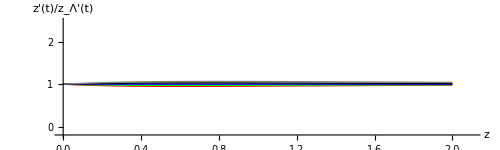

```mathematica
pltdzConFunc=Flatten[Table[dzCon[z,w0]/dz[z,1],{w0,liEoS}]];
pltdzCon=Plot[pltdzConFunc,{z,0,2},PlotRange->pltRange,AxesOrigin->axesOrigin,AxesLabel->{"z","z'(t)/z_Λ'(t)"},AspectRatio->aspectRatioCon,ImageSize->imgSize,ImagePadding->imgPadding,PlotStyle->pltStyleCon]
```

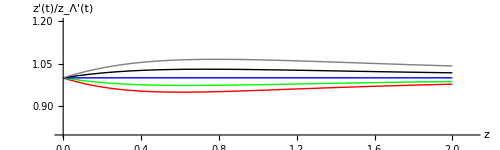

```mathematica
Show[pltdzCon,PlotRange->{{0,2.1},{0.8,1.2}},AxesOrigin->{0,0.8}]
```

NIntegrate::nlim: tmp = z is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

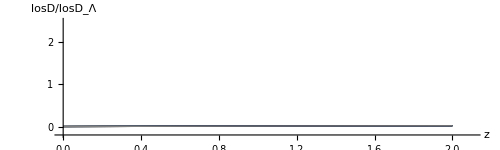

```mathematica
pltlosDistanceConFunc=Flatten[Table[losDistanceCon[z,w0],{w0,liEoS}]];
pltlosDistanceCon=Plot[pltlosDistanceConFunc,{z,0,2},PlotRange->pltRange,AxesOrigin->axesOrigin,AxesLabel->{"z","losD/losD_Λ"},AspectRatio->aspectRatioCon,ImageSize->imgSize,ImagePadding->imgPadding,PlotStyle->pltStyleCon]
```

Change the plot range to see it clearly.

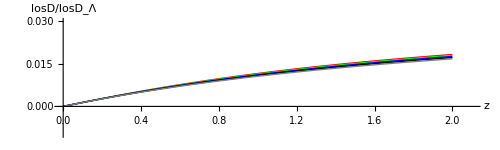

```mathematica
Show[pltlosDistanceCon,PlotRange->{{0,2.1},{-0.01,0.03}},AxesOrigin->{0,0}]
```

Angular diameter diatence

NIntegrate::nlim: tmp = z is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

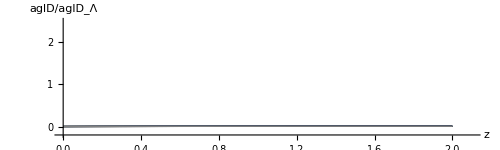

```mathematica
pltAglDistanceConFunc=Flatten[Table[aglDistanceCon[z,w0],{w0,liEoS}]];
pltAglDistanceCon=Plot[pltAglDistanceConFunc,{z,0,2},PlotRange->pltRange,AxesOrigin->axesOrigin,AxesLabel->{"z","aglD/aglD_Λ"},AspectRatio->aspectRatioCon,ImageSize->imgSize,ImagePadding->imgPadding,PlotStyle->pltStyleCon]
```

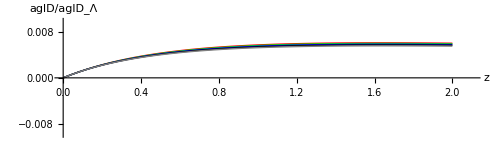

```mathematica
Show[pltAglDistanceCon,PlotRange->{{0,2.1},{-0.01,0.01}},AxesOrigin->{0,0}]
```

NIntegrate::nlim: tmp = z is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

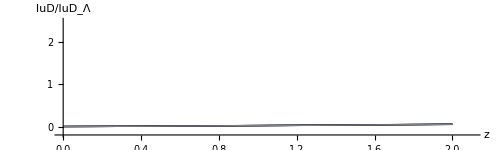

```mathematica
pltluDistanceConFunc=Flatten[Table[luDistanceCon[z,w0],{w0,liEoS}]];
pltluDistanceCon=Plot[pltluDistanceConFunc,{z,0,2},PlotRange->pltRange,AxesOrigin->axesOrigin,AxesLabel->{"z","luD/luD_Λ"},AspectRatio->aspectRatioCon,ImageSize->imgSize,ImagePadding->imgPadding,PlotStyle->pltStyleCon]
```

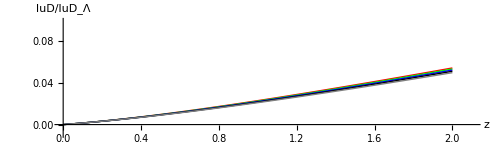

```mathematica
Show[pltluDistanceCon,PlotRange->{{0,2.1},{-0.01,0.1}},AxesOrigin->{0,0}]
```

NIntegrate::nlim: tmp = z is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

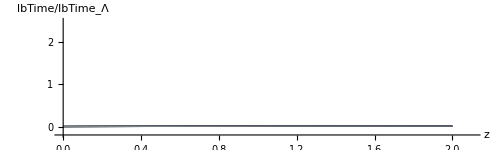

```mathematica
pltlbTimeConFunc=Flatten[Table[lbTimeCon[z,w0],{w0,liEoS}]];
pltlbTimeCon=Plot[pltlbTimeConFunc,{z,0,2},PlotRange->pltRange,AxesOrigin->axesOrigin,AxesLabel->{"z","lbTime/lbTime_Λ"},AspectRatio->aspectRatioCon,ImageSize->imgSize,ImagePadding->imgPadding,PlotStyle->pltStyleCon]
```

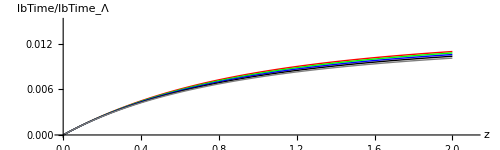

```mathematica
Show[pltlbTimeCon,PlotRange->{{0,2.1},{-0.0,0.015}},AxesOrigin->{0,0}]
```

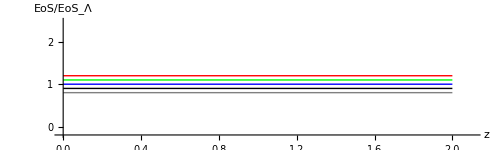

```mathematica
pltEoSConFunc=Flatten[Table[w0/(-1),{w0,liEoS}]];
pltEoSCon=Plot[pltEoSConFunc,{z,0,2},PlotRange->pltRange,AxesOrigin->axesOrigin,AxesLabel->{"z","EoS/EoS_Λ"},AspectRatio->aspectRatioCon,ImageSize->500,ImagePadding->imgPadding,PlotStyle->pltStyleCon]
```

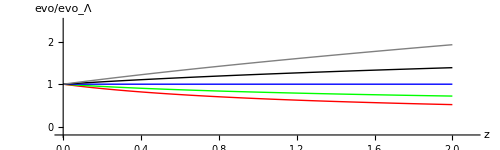

```mathematica
pltevoConFunc=Flatten[Table[evoCon[z,w0],{w0,liEoS}]];
pltevoCon=Plot[pltevoConFunc,{z,0,2},PlotRange->pltRange,AxesOrigin->axesOrigin,AxesLabel->{"z","evo/evo_Λ"},AspectRatio->aspectRatioCon,ImageSize->imgSizeCon,ImagePadding->imgPadding,PlotStyle->pltStyleCon]
```

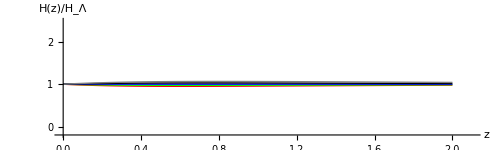

```mathematica
pltHubbleConFunc=Flatten[Table[hubbleCon[z,w0]/hubbleLCDM[z],{w0,liEoS}]];
pltHubbleCon=Plot[pltHubbleConFunc,{z,0,2},PlotRange->pltRange,AxesOrigin->axesOrigin,AxesLabel->{"z","H(z)/H_Λ"},AspectRatio->aspectRatioCon,ImageSize->imgSizeCon,ImagePadding->imgPadding,PlotStyle->pltStyleCon]
```

Combine the plots

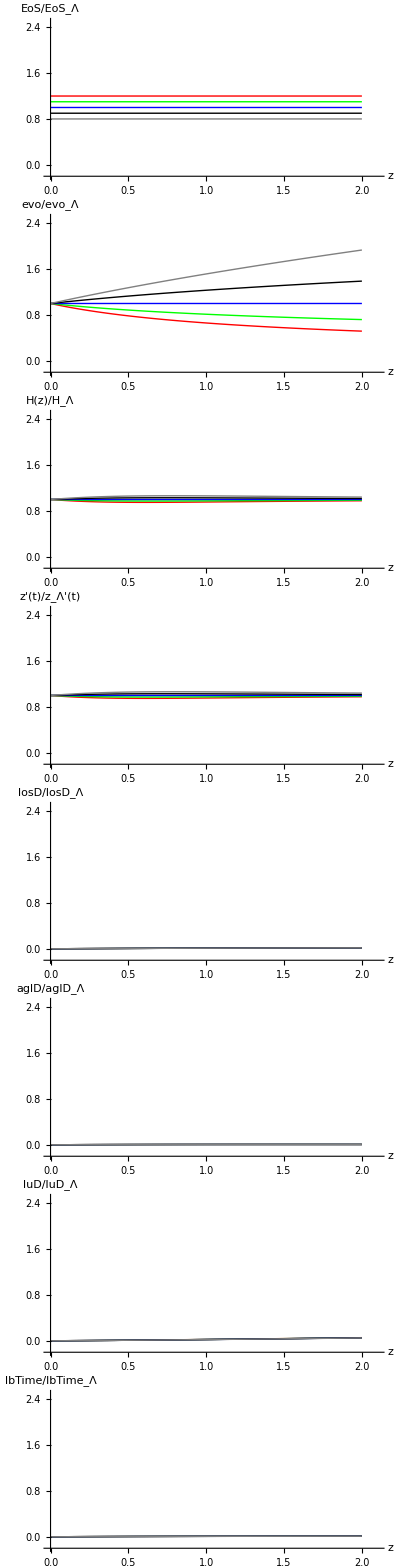

```mathematica
pltCon=Grid[{{pltEoSCon},{pltevoCon},
{pltHubbleCon},
{pltdzCon},
{pltlosDistanceCon},
{pltAglDistanceCon},
{pltluDistanceCon},
{pltlbTimeCon}}]
```

### Family 1

List of equation of state parameters

```mathematica
liEoSF10=Table[w0,{w0,{-1.2,-1.1,-1.0,-0.9,-0.8}}];
liEoSF11=Table[w1,{w1,{-0.1,0,0.1}}];
```

```mathematica
pltRangeF1={{0,2.1},{-0.2,2.5}}
```

{{0,2.1},{-0.2,2.5}}

```mathematica
axesOriginF1={0,-0.2}
```

{0,-0.2}

```mathematica
imgPaddingF1={{30,30},{30,30}}
```

{{30,30},{30,30}}

```mathematica
imgSizeF1=500
```

500

```mathematica
aspectRatioF1=0.3
```

0.3

```mathematica
pltStyleF1={Red,Green,Blue,Black,Gray,Cyan,Magenta,Yellow,Brown,Orange,Pink,Purple,LightRed,LightGreen,LightBlue,LightGray,LightCyan,LightMagenta,LightYellow,LightBrown,LightOrange,LightPurple}
```

{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],GrayLevel[0],GrayLevel[0.5],RGBColor[0,1,1],RGBColor[1,0,1],RGBColor[1,1,0],RGBColor[0.6,0.4,0.2],RGBColor[1,0.5,0],RGBColor[1,0.5,0.5],RGBColor[0.5,0,0.5],RGBColor[1,0.85,0.85],RGBColor[0.88,1,0.88],RGBColor[0.87,0.94,1],GrayLevel[0.85],RGBColor[0.9,1,1],RGBColor[1,0.9,1],RGBColor[1,1,0.85],RGBColor[0.94,0.91,0.88],RGBColor[1,0.9,0.8],RGBColor[0.94,0.88,0.94]}

Plots

Line of Sight comoving distance

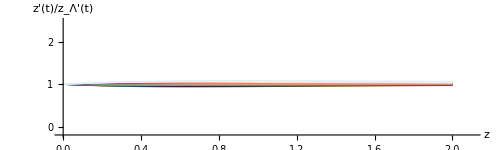

```mathematica
pltdzF1Func=Flatten[Table[dzF1[z,1,w0,w1]/dz[z,1],{w0,liEoSF10},{w1,liEoSF11}]];
pltdzF1=Plot[pltdzF1Func,{z,0,2},PlotRange->pltRangeF1,AxesOrigin->axesOriginF1,AxesLabel->{"z","z'(t)/z_Λ'(t)"},AspectRatio->aspectRatioF1,ImageSize->imgSizeF1,ImagePadding->imgPaddingF1,PlotStyle->pltStyleF1]
```

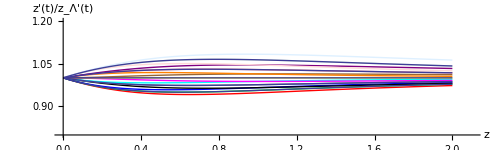

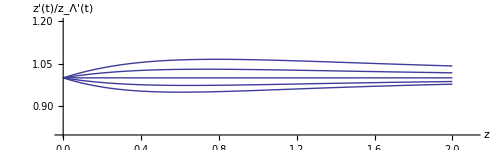

```mathematica
Show[{pltdzF1,pltdzCon},PlotRange->{{0,2.1},{0.8,1.2}},AxesOrigin->{0,0.8}]
Show[pltdzCon,PlotRange->{{0,2.1},{0.8,1.2}},AxesOrigin->{0,0.8}]
```

NIntegrate::nlim: tmp = z is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

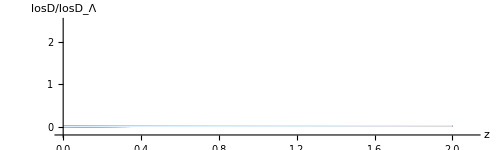

```mathematica
pltlosDistanceF1Func=Flatten[Table[losDistanceF1[z,1,w0,w1],{w0,liEoSF10},{w1,liEoSF11}]];
pltlosDistanceF1=Plot[pltlosDistanceF1Func,{z,0,2},PlotRange->pltRangeF1,AxesOrigin->axesOriginF1,AxesLabel->{"z","losD/losD_Λ"},AspectRatio->aspectRatioF1,ImageSize->imgSizeF1,ImagePadding->imgPaddingF1,PlotStyle->pltStyleF1]
```

Change the plot range to see it clearly.

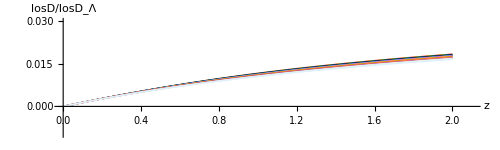

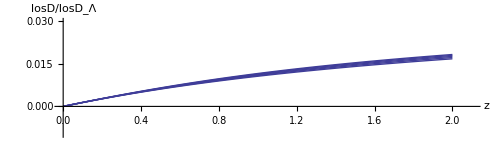

```mathematica
Show[pltlosDistanceF1,PlotRange->{{0,2.1},{-0.01,0.03}},AxesOrigin->{0,0}]
Show[pltlosDistanceCon,PlotRange->{{0,2.1},{-0.01,0.03}},AxesOrigin->{0,0}]
```

Angular diameter diatence

NIntegrate::nlim: tmp = z is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

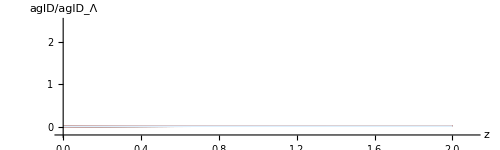

```mathematica
pltAglDistanceF1Func=Flatten[Table[aglDistanceF1[z,1,w0,w1],{w0,liEoSF10},{w1,liEoSF11}]];
pltAglDistanceF1=Plot[pltAglDistanceF1Func,{z,0,2},PlotRange->pltRangeF1,AxesOrigin->axesOriginF1,AxesLabel->{"z","aglD/aglD_Λ"},AspectRatio->aspectRatioF1,ImageSize->imgSizeF1,ImagePadding->imgPaddingF1,PlotStyle->pltStyleF1]
```

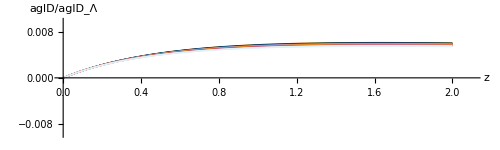

```mathematica
Show[pltAglDistanceF1,PlotRange->{{0,2.1},{-0.01,0.01}},AxesOrigin->{0,0}]
```

NIntegrate::nlim: tmp = z is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

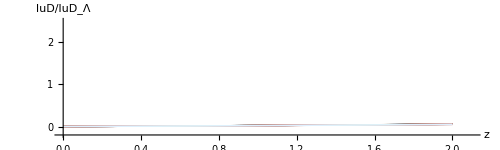

```mathematica
pltluDistanceF1Func=Flatten[Table[luDistanceF1[z,1,w0,w1],{w0,liEoSF10},{w1,liEoSF11}]];
pltluDistanceF1=Plot[pltluDistanceF1Func,{z,0,2},PlotRange->pltRangeF1,AxesOrigin->axesOriginF1,AxesLabel->{"z","luD/luD_Λ"},AspectRatio->aspectRatioF1,ImageSize->imgSizeF1,ImagePadding->imgPaddingF1,PlotStyle->pltStyleF1]
```

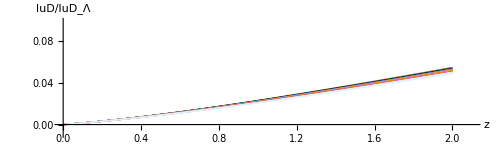

```mathematica
Show[pltluDistanceF1,PlotRange->{{0,2.1},{-0.01,0.1}},AxesOrigin->{0,0}]
```

NIntegrate::nlim: tmp = z is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

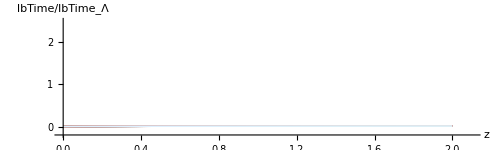

```mathematica
pltlbTimeF1Func=Flatten[Table[lbTimeF1[z,1,w0,w1],{w0,liEoSF10},{w1,liEoSF11}]];
pltlbTimeF1=Plot[pltlbTimeF1Func,{z,0,2},PlotRange->pltRangeF1,AxesOrigin->axesOriginF1,AxesLabel->{"z","lbTime/lbTime_Λ"},AspectRatio->aspectRatioF1,ImageSize->imgSizeF1,ImagePadding->imgPaddingF1,PlotStyle->pltStyleF1]
```

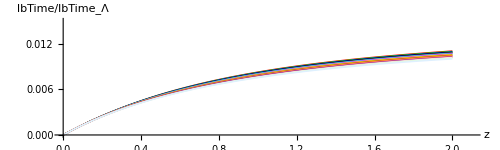

```mathematica
Show[pltlbTimeF1,PlotRange->{{0,2.1},{-0.0,0.015}},AxesOrigin->{0,0}]
```

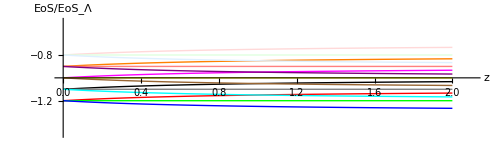

```mathematica
pltEoSF1Func=Flatten[Table[w0+w1(z/(1+z))^1/(-1),{w0,liEoSF10},{w1,liEoSF11}]];
pltEoSF1=Plot[pltEoSF1Func,{z,0,2},PlotRange->{{0,2.1},{-1.5,-0.5}},AxesOrigin->{0,-1},AxesLabel->{"z","EoS/EoS_Λ"},AspectRatio->aspectRatioF1,ImageSize->imgSizeF1,ImagePadding->imgPaddingF1,PlotStyle->pltStyleF1]
```

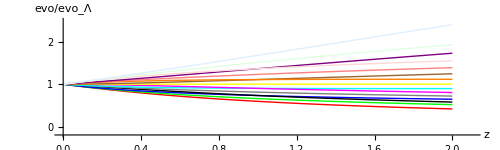

```mathematica
pltevoF1Func=Flatten[Table[evoF1[z,1,w0,w1],{w0,liEoSF10},{w1,liEoSF11}]];
pltevoF1=Plot[pltevoF1Func,{z,0,2},PlotRange->pltRangeF1,AxesOrigin->axesOriginF1,AxesLabel->{"z","evo/evo_Λ"},AspectRatio->aspectRatioF1,ImageSize->imgSizeF1,ImagePadding->imgPaddingF1,PlotStyle->pltStyleF1]
```

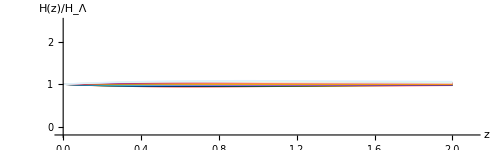

```mathematica
pltHubbleF1Func=Flatten[Table[hubbleF1[z,1,w0,w1]/hubbleLCDM[z],{w0,liEoSF10},{w1,liEoSF11}]];
pltHubbleF1=Plot[pltHubbleF1Func,{z,0,2},PlotRange->pltRangeF1,AxesOrigin->axesOriginF1,AxesLabel->{"z","H(z)/H_Λ"},AspectRatio->aspectRatioF1,ImageSize->imgSizeF1,ImagePadding->imgPaddingF1,PlotStyle->pltStyleF1]
```

Combine the plots

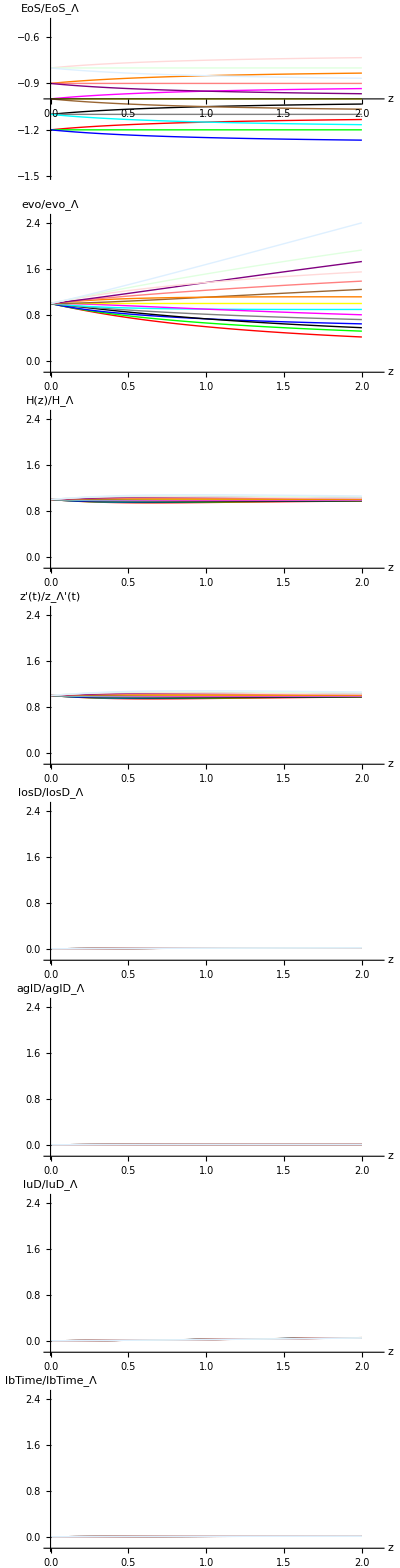

```mathematica
pltF1=Grid[{{pltEoSF1},{pltevoF1},
{pltHubbleF1},
{pltdzF1},
{pltlosDistanceF1},
{pltAglDistanceF1},
{pltluDistanceF1},
{pltlbTimeF1}}]
```

### Family 2

List of equation of state parameters

```mathematica
liEoSF20=Table[w0,{w0,{-1.2,-1.1,-1.0,-0.9,-0.8}}];
liEoSF21=Table[w1,{w1,{-0.1,0,0.1}}];
```

```mathematica
pltRangeF2={{0,2.1},{-0.2,2.5}}
```

{{0,2.1},{-0.2,2.5}}

```mathematica
axesOriginF2={0,-0.2}
```

{0,-0.2}

```mathematica
imgPaddingF2={{30,30},{30,30}}
```

{{30,30},{30,30}}

```mathematica
imgSizeF2=500
```

500

```mathematica
aspectRatioF2=0.3
```

0.3

```mathematica
pltStyleF2={Red,Green,Blue,Black,Gray,Cyan,Magenta,Yellow,Brown,Orange,Pink,Purple,LightRed,LightGreen,LightBlue,LightGray,LightCyan,LightMagenta,LightYellow,LightBrown,LightOrange,LightPurple}
```

{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],GrayLevel[0],GrayLevel[0.5],RGBColor[0,1,1],RGBColor[1,0,1],RGBColor[1,1,0],RGBColor[0.6,0.4,0.2],RGBColor[1,0.5,0],RGBColor[1,0.5,0.5],RGBColor[0.5,0,0.5],RGBColor[1,0.85,0.85],RGBColor[0.88,1,0.88],RGBColor[0.87,0.94,1],GrayLevel[0.85],RGBColor[0.9,1,1],RGBColor[1,0.9,1],RGBColor[1,1,0.85],RGBColor[0.94,0.91,0.88],RGBColor[1,0.9,0.8],RGBColor[0.94,0.88,0.94]}

Plots

Line of Sight comoving distance

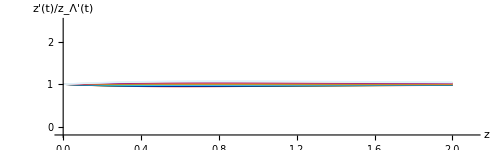

```mathematica
pltdzF2Func=Flatten[Table[dzF2[z,2,w0,w1]/dz[z,1],{w0,liEoSF20},{w1,liEoSF21}]];
pltdzF2=Plot[pltdzF2Func,{z,0,2},PlotRange->pltRangeF2,AxesOrigin->axesOriginF2,AxesLabel->{"z","z'(t)/z_Λ'(t)"},AspectRatio->aspectRatioF2,ImageSize->imgSizeF2,ImagePadding->imgPaddingF2,PlotStyle->pltStyleF2]
```

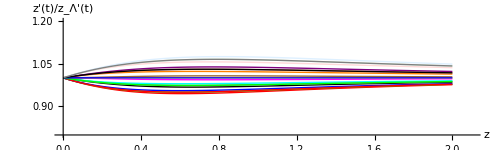

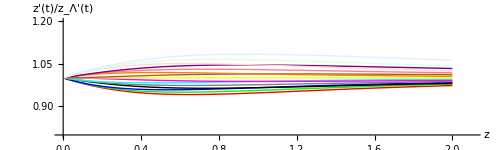

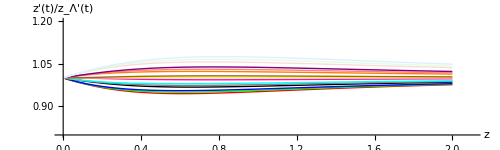

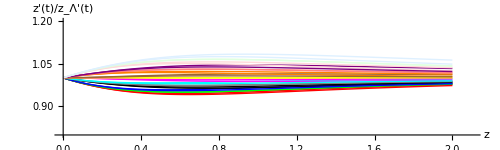

-Graphics-

```mathematica
Show[{pltdzF2,pltdzCon},PlotRange->{{0,2.1},{0.8,1.2}},AxesOrigin->{0,0.8}]
Show[pltdzF1,PlotRange->{{0,2.1},{0.8,1.2}},AxesOrigin->{0,0.8}]
Show[pltdzF2,PlotRange->{{0,2.1},{0.8,1.2}},AxesOrigin->{0,0.8}]
Show[{pltdzF1,pltdzF2},PlotRange->{{0,2.1},{0.8,1.2}},AxesOrigin->{0,0.8}]
Show[pltdzCon,PlotRange->{{0,2.1},{0.8,1.2}},AxesOrigin->{0,0.8}]
```

NIntegrate::nlim: tmp = z is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

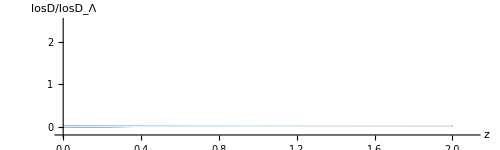

```mathematica
pltlosDistanceF2Func=Flatten[Table[losDistanceF2[z,2,w0,w1],{w0,liEoSF20},{w1,liEoSF21}]];
pltlosDistanceF2=Plot[pltlosDistanceF2Func,{z,0,2},PlotRange->pltRangeF2,AxesOrigin->axesOriginF2,AxesLabel->{"z","losD/losD_Λ"},AspectRatio->aspectRatioF2,ImageSize->imgSizeF2,ImagePadding->imgPaddingF2,PlotStyle->pltStyleF2]
```

Change the plot range to see it clearly.

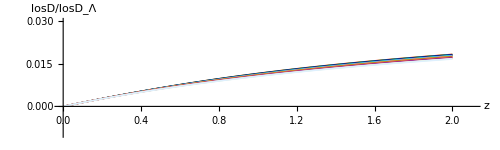

-Graphics-

```mathematica
Show[pltlosDistanceF2,PlotRange->{{0,2.1},{-0.01,0.03}},AxesOrigin->{0,0}]
Show[pltlosDistanceCon,PlotRange->{{0,2.1},{-0.01,0.03}},AxesOrigin->{0,0}]
```

Angular diameter diatence

NIntegrate::nlim: tmp = z is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

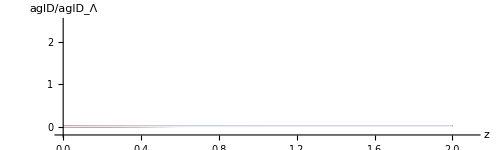

```mathematica
pltAglDistanceF2Func=Flatten[Table[aglDistanceF2[z,2,w0,w1],{w0,liEoSF20},{w1,liEoSF21}]];
pltAglDistanceF2=Plot[pltAglDistanceF2Func,{z,0,2},PlotRange->pltRangeF2,AxesOrigin->axesOriginF2,AxesLabel->{"z","aglD/aglD_Λ"},AspectRatio->aspectRatioF2,ImageSize->imgSizeF2,ImagePadding->imgPaddingF2,PlotStyle->pltStyleF2]
```

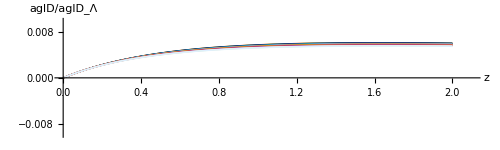

```mathematica
Show[pltAglDistanceF2,PlotRange->{{0,2.1},{-0.01,0.01}},AxesOrigin->{0,0}]
```

NIntegrate::nlim: tmp = z is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

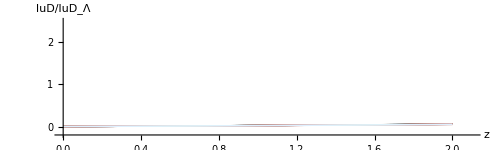

```mathematica
pltluDistanceF2Func=Flatten[Table[luDistanceF2[z,2,w0,w1],{w0,liEoSF20},{w1,liEoSF21}]];
pltluDistanceF2=Plot[pltluDistanceF2Func,{z,0,2},PlotRange->pltRangeF2,AxesOrigin->axesOriginF2,AxesLabel->{"z","luD/luD_Λ"},AspectRatio->aspectRatioF2,ImageSize->imgSizeF2,ImagePadding->imgPaddingF2,PlotStyle->pltStyleF2]
```

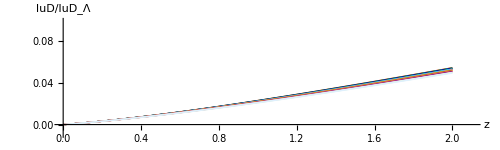

```mathematica
Show[pltluDistanceF2,PlotRange->{{0,2.1},{-0.01,0.1}},AxesOrigin->{0,0}]
```

NIntegrate::nlim: tmp = z is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

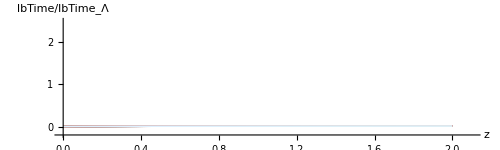

```mathematica
pltlbTimeF2Func=Flatten[Table[lbTimeF2[z,2,w0,w1],{w0,liEoSF20},{w1,liEoSF21}]];
pltlbTimeF2=Plot[pltlbTimeF2Func,{z,0,2},PlotRange->pltRangeF2,AxesOrigin->axesOriginF2,AxesLabel->{"z","lbTime/lbTime_Λ"},AspectRatio->aspectRatioF2,ImageSize->imgSizeF2,ImagePadding->imgPaddingF2,PlotStyle->pltStyleF2]
```

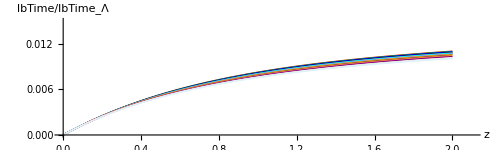

```mathematica
Show[pltlbTimeF2,PlotRange->{{0,2.1},{-0.0,0.015}},AxesOrigin->{0,0}]
```

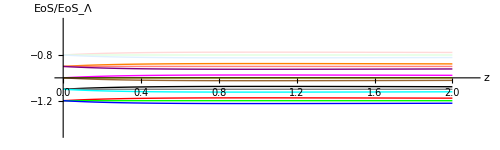

```mathematica
pltEoSF2Func=Flatten[Table[w0+w1 z/(1+z)^2/(-1),{w0,liEoSF20},{w1,liEoSF21}]];
pltEoSF2=Plot[pltEoSF2Func,{z,0,2},PlotRange->{{0,2.1},{-1.5,-0.5}},AxesOrigin->{0,-1},AxesLabel->{"z","EoS/EoS_Λ"},AspectRatio->aspectRatioF2,ImageSize->imgSizeF2,ImagePadding->imgPaddingF2,PlotStyle->pltStyleF2]
```

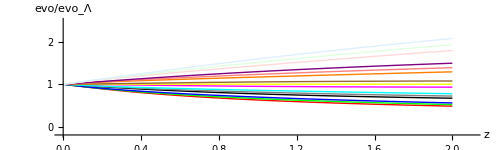

```mathematica
pltevoF2Func=Flatten[Table[evoF2[z,2,w0,w1],{w0,liEoSF20},{w1,liEoSF21}]];
pltevoF2=Plot[pltevoF2Func,{z,0,2},PlotRange->pltRangeF2,AxesOrigin->axesOriginF2,AxesLabel->{"z","evo/evo_Λ"},AspectRatio->aspectRatioF2,ImageSize->imgSizeF2,ImagePadding->imgPaddingF2,PlotStyle->pltStyleF2]
```

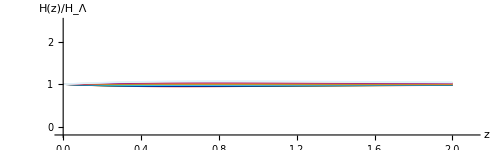

```mathematica
pltHubbleF2Func=Flatten[Table[hubbleF2[z,2,w0,w1]/hubbleLCDM[z],{w0,liEoSF20},{w1,liEoSF21}]];
pltHubbleF2=Plot[pltHubbleF2Func,{z,0,2},PlotRange->pltRangeF2,AxesOrigin->axesOriginF2,AxesLabel->{"z","H(z)/H_Λ"},AspectRatio->aspectRatioF2,ImageSize->imgSizeF2,ImagePadding->imgPaddingF2,PlotStyle->pltStyleF2]
```

Combine the plots

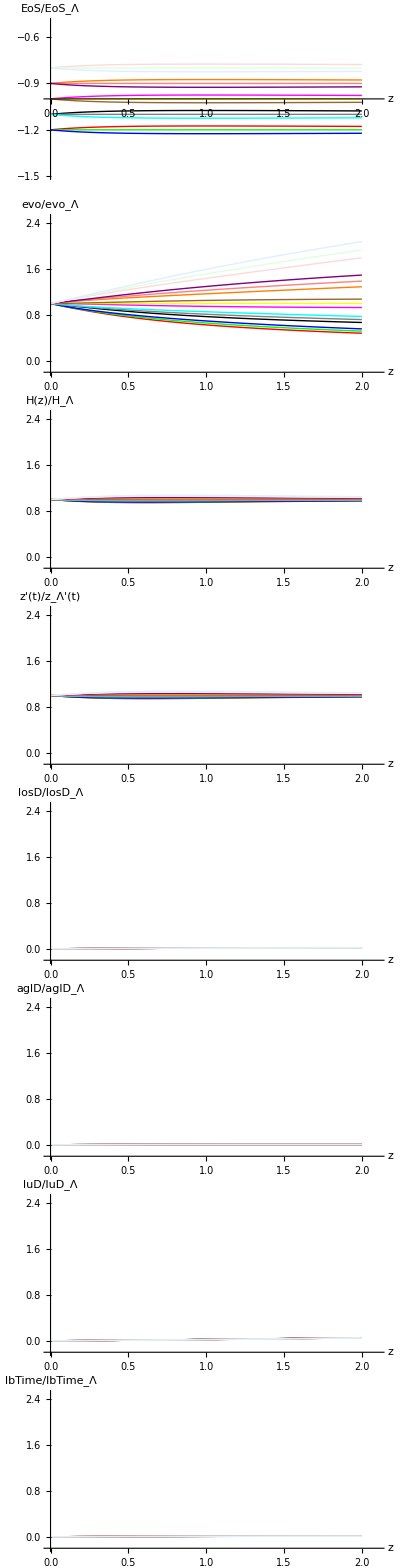

```mathematica
pltF2=Grid[{{pltEoSF2},{pltevoF2},
{pltHubbleF2},
{pltdzF2},
{pltlosDistanceF2},
{pltAglDistanceF2},
{pltluDistanceF2},
{pltlbTimeF2}}]
```

### Compare

```mathematica
Grid[{{pltCon,pltF1,pltF2}}]
```

-Graphics- | -Graphics- | -Graphics-

## Drafts

```mathematica
hubbleCon[1,-0.9]
```

124.174

```mathematica
,PlotRange->{{0,2.1},{0.85,1.25}}
```

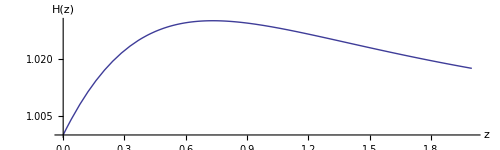
{0.,-Graphics-}

```mathematica
Plot[Table[hubbleCon[z,w0]/hubbleLCDM[z],{w0,{-0.9}}],{z,0,2},AxesLabel->{"z","H(z)"},AspectRatio->0.3,ImageSize->500]//Timing
```

```mathematica
Manipulate[Plot[dzCon[z,w0]/dzCon[z,-1],{z,0,2},AxesLabel->{"z","H(z)"},AspectRatio->0.3,ImageSize->500],{w0,-1.5,-0.5}]
```

CPL

```mathematica
eos1[z_,n_,w0_,w1_]:=w0+w1(z/(1+z))^n
```

```mathematica
evo1[z_,n_,w0_,w1_]=evo[z,eos1[tmp,n,w0,w1]]
```

ConditionalExpression[ⅇ^(3 (-(-1)^-n w1 Beta[-z,1+n,-n]+(1+w0) Log[1+z])),Re[n]>-1&&z>0]

```mathematica
eosCPL1[z_]=eos[z,1,-0.9,0.1]
```

eos[z,1,-0.9,0.1]

```mathematica
evoCPL1[z_]=Simplify[evo[z,eosCPL1[z]],Reals]
```

ConditionalExpression[(1+z)^(3 (1+eos[z,1,-0.9,0.1])),Re[z]≥-1||z∉Reals]

```mathematica
hubbleCPL1[z]=hubble[z,evoCPL1[z]]
```

ConditionalExpression[71 √(0.27 (1+z)^3+0.73 (1+z)^(3 (1+eos[z,1,-0.9,0.1]))),Re[z]≥-1||z∉Reals]